```mathematica
import[file_]:=Module[{imp,toe,data,combined,lasts},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/"~~ToString@file];
toe=ToExpression/@StringSplit[imp];
data=Partition[toe,2];
combined=Gather[data,#1[[1]]==#2[[1]]&];
lasts={#[[1,1]],Max@#[[All,2]]}&/@combined;
{StringSplit[file,"_"][[1]],lasts}
]
```

```mathematica
SetDirectory["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data"]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data

```mathematica
data=import/@FileNames["*.txt"]
```

{{cache-lock-tt,{{1,1009},{2,2007},{3,2020},{4,2044},{5,2162},{6,2336},{7,3249},{8,4219},{9,5389},{10,9588},{11,14964},{12,20337},{13,47144},{14,56539}}},{cache-lock-tt,{{1,11},{2,2200},{3,3704},{4,3711},{5,3726},{6,3758},{7,4382},{8,5920},{9,6255},{10,7713},{11,9835},{12,29416},{13,57336},{14,57337}}},{cache-lock-tt,{{1,14},{2,2011},{3,2034},{4,5702},{5,6902},{6,7031},{7,7282},{8,7904},{9,14413},{10,16400},{11,37193},{12,56446},{13,56446}}},{cache-lock-tt,{{1,15},{2,2012},{3,2039},{4,2076},{5,12297},{6,23271},{7,23281},{8,25965},{9,57970},{13,57971}}},{cache-tt,{{1,6},{2,11},{3,22},{4,42},{5,169},{6,620},{7,1245},{8,2956},{9,5461},{10,10891},{11,13359},{12,18523},{13,46890},{14,59416}}},{cache-tt,{}},{cache-tt,{}},{cache-tt,{}},{global-smp,{{1,1},{2,1},{3,2},{4,2},{5,4},{6,8},{7,11},{8,16},{9,31},{10,57},{11,109},{12,153},{13,442},{14,570},{15,872},{16,1210},{17,1655},{18,1797},{19,2970},{20,4679},{21,5848},{22,7386},{23,13312},{24,15348},{25,29945},{26,49605},{27,55682},{28,59777}}},{global-smp,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,6},{7,10},{8,11},{9,24},{10,66},{11,91},{12,149},{13,308},{14,531},{15,678},{16,713},{17,806},{18,1356},{19,2033},{20,2514},{21,3926},{22,4602},{23,5778},{24,8116},{25,18735},{26,25571},{27,33094},{28,42779},{29,55154},{30,59843}}},{global-smp,{{1,1},{2,2},{3,2},{4,2},{5,4},{6,6},{7,7},{8,14},{9,26},{10,45},{11,94},{12,243},{13,348},{14,385},{15,462},{16,624},{17,871},{18,1139},{19,1330},{20,1452},{21,1863},{22,5336},{23,10725},{24,13290},{25,15507},{26,21761},{27,31567},{28,47625},{29,59838}}},{global-smp,{{1,2},{2,2},{3,3},{4,3},{5,7},{6,8},{7,12},{8,21},{9,49},{10,109},{11,145},{12,232},{13,379},{14,408},{15,696},{16,823},{17,899},{18,1671},{19,1938},{20,2227},{21,2660},{22,4728},{23,5824},{24,8740},{25,9874},{26,15654},{27,20383},{28,27533},{29,35922},{30,59842}}},{global-smp-opt,{{1,1},{2,1},{3,2},{4,2},{5,4},{6,8},{7,11},{8,16},{9,31},{10,57},{11,110},{12,155},{13,446},{14,576},{15,882},{16,1221},{17,1668},{18,1810},{19,2992},{20,4712},{21,5888},{22,7603},{23,13139},{24,14626},{25,18470},{26,23980},{27,45848},{28,55898},{29,59792}}},{global-smp-opt,{{1,2},{2,2},{3,3},{4,3},{5,5},{6,7},{7,14},{8,20},{9,33},{10,72},{11,149},{12,260},{13,381},{14,476},{15,602},{16,837},{17,950},{18,1270},{19,1861},{20,2260},{21,2510},{22,3139},{23,7323},{24,9005},{25,11629},{26,23316},{27,41501},{28,59845},{29,59844}}},{global-smp-opt,{{1,2},{2,2},{3,2},{4,3},{5,6},{6,8},{7,13},{8,18},{9,33},{10,70},{11,149},{12,164},{13,334},{14,418},{15,629},{16,757},{17,843},{18,1091},{19,1646},{20,2843},{21,4085},{22,5554},{23,6772},{24,11794},{25,17929},{26,22847},{27,26256},{28,40825},{29,59845},{30,59844}}},{global-smp-opt,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,7},{7,15},{8,23},{9,37},{10,71},{11,90},{12,230},{13,340},{14,418},{15,524},{16,1004},{17,1111},{18,1341},{19,1667},{20,2022},{21,2983},{22,4993},{23,7646},{24,14008},{25,22893},{26,24892},{27,32086},{28,38362},{29,59843},{30,59842}}},{irreversible-tt,{{1,11},{2,19},{3,53},{4,107},{5,423},{6,1243},{7,2715},{8,4199},{9,12491},{10,20358},{11,59427}}},{irreversible-tt,{}},{irreversible-tt,{}},{irreversible-tt,{}},{naive-tt,{{1,11},{2,20},{3,50},{4,99},{5,562},{6,841},{7,1331},{8,3839},{9,16334},{10,22169},{11,55393},{12,59331}}},{naive-tt,{}},{naive-tt,{}},{naive-tt,{}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,7},{7,9},{8,13},{9,24},{10,44},{11,83},{12,116},{13,343},{14,449},{15,714},{16,1027},{17,1454},{18,1590},{19,2691},{20,3670},{21,4303},{22,5920},{23,11457},{24,23843},{25,30275},{26,39946},{27,53693},{28,59985}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,3},{5,4},{6,6},{7,12},{8,18},{9,31},{10,82},{11,198},{12,251},{13,394},{14,465},{15,623},{16,692},{17,1094},{18,1327},{19,2172},{20,2407},{21,2681},{22,3375},{23,4718},{24,5766},{25,7962},{26,26860},{27,33524},{28,54145},{29,59985}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,3},{6,8},{7,9},{8,15},{9,39},{10,67},{11,111},{12,229},{13,365},{14,495},{15,582},{16,744},{17,972},{18,1108},{19,1453},{20,1663},{21,2384},{22,3652},{23,4254},{24,9303},{25,17919},{26,23317},{27,32889},{28,46007},{29,58059},{30,59984}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,3},{5,4},{6,7},{7,8},{8,20},{9,35},{10,100},{11,125},{12,197},{13,325},{14,399},{15,534},{16,691},{17,795},{18,955},{19,1219},{20,1346},{21,2043},{22,4055},{23,4452},{24,12823},{25,17212},{26,20307},{27,23791},{28,39113},{29,55547},{30,59983}}}}

```mathematica
medians=Gather[data,#1[[1]]==#2[[1]]&]//{#[[1,1]],Sequence@@#&/@#[[All,2,All]]}&/@#&//{#[[1]],{#[[1,1]],Median@#[[All,2]]}&/@Gather[#[[2]],#[[1]]==#2[[1]]&]}&/@#&
```

{{cache-lock-tt,{{1,29/2},{2,4023/2},{3,4073/2},{4,5787/2},{5,5314},{6,10789/2},{7,5832},{8,6912},{9,10334},{10,9588},{11,14964},{12,29416},{13,56891},{14,56938}}},{cache-tt,{{1,6},{2,11},{3,22},{4,42},{5,169},{6,620},{7,1245},{8,2956},{9,5461},{10,10891},{11,13359},{12,18523},{13,46890},{14,59416}}},{global-smp,{{1,3/2},{2,2},{3,2},{4,2},{5,4},{6,7},{7,21/2},{8,15},{9,57/2},{10,123/2},{11,203/2},{12,385/2},{13,727/2},{14,939/2},{15,687},{16,768},{17,885},{18,3027/2},{19,3971/2},{20,4741/2},{21,3293},{22,5032},{23,16549/2},{24,11015},{25,17121},{26,23666},{27,64661/2},{28,45202},{29,55154},{30,119685/2}}},{global-smp-opt,{{1,2},{2,2},{3,2},{4,5/2},{5,9/2},{6,15/2},{7,27/2},{8,19},{9,33},{10,141/2},{11,259/2},{12,197},{13,721/2},{14,447},{15,1231/2},{16,1841/2},{17,2061/2},{18,2611/2},{19,1764},{20,5103/2},{21,3534},{22,10547/2},{23,14969/2},{24,12901},{25,36399/2},{26,23648},{27,73587/2},{28,96723/2},{29,119687/2},{30,59843}}},{irreversible-tt,{{1,11},{2,19},{3,53},{4,107},{5,423},{6,1243},{7,2715},{8,4199},{9,12491},{10,20358},{11,59427}}},{naive-tt,{{1,11},{2,20},{3,50},{4,99},{5,562},{6,841},{7,1331},{8,3839},{9,16334},{10,22169},{11,55393},{12,59331}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,5/2},{5,4},{6,7},{7,9},{8,33/2},{9,33},{10,149/2},{11,118},{12,213},{13,354},{14,457},{15,1205/2},{16,718},{17,1033},{18,2435/2},{19,3625/2},{20,2035},{21,5065/2},{22,7707/2},{23,4585},{24,11063},{25,35131/2},{26,50177/2},{27,66413/2},{28,50076},{29,58059},{30,119967/2}}}}

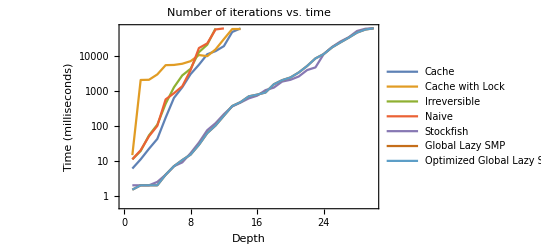

```mathematica
ttdGraph=Module[{d,cache,cachelock,globallazysmp,irreversible,naive,stockfish,legends,labels,lp,joined,globalopt,alldata},
d=medians;
cache=Select[d,#[[1]]=="cache-tt"&][[1,2]];
cachelock=Select[d,#[[1]]=="cache-lock-tt"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible-tt"&][[1,2]];
naive=Select[d,#[[1]]=="naive-tt"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish-master"&][[1,2]];
globallazysmp=Select[d,#[[1]]=="global-smp"&][[1,2]];
globalopt=Select[d,#[[1]]=="global-smp"&][[1,2]];

legends={"Cache","Cache with Lock","Irreversible","Naive","Stockfish","Global Lazy SMP","Optimized Global Lazy SMP"};
alldata={cache,cachelock,irreversible,naive,stockfish,globallazysmp,globalopt};
labels={"Depth","Time (milliseconds)"};
lp=ListLogPlot[alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[alldata,PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

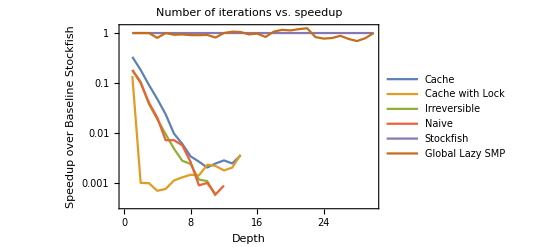

```mathematica
ttdSpeedupGraph=Module[{d,cache,cachelock,globallazysmp,irreversible,naive,stockfish,legends,labels,lp,joined,tS,speedup,alldata},
d=medians;
cache=Select[d,#[[1]]=="cache-tt"&][[1,2]];
cachelock=Select[d,#[[1]]=="cache-lock-tt"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible-tt"&][[1,2]];
naive=Select[d,#[[1]]=="naive-tt"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish-master"&][[1,2]];
globallazysmp=Select[d,#[[1]]=="global-smp"&][[1,2]];
tS=stockfish[[All,2]];
speedup[data_]:=MapThread[{#[[1]],#2/#[[2]]}&,{data,tS[[;;Length@data]]}];

legends={"Cache","Cache with Lock","Irreversible","Naive","Stockfish","Global Lazy SMP"};
labels={"Depth","Speedup over Baseline Stockfish"};
alldata={cache,cachelock,irreversible,naive,stockfish,globallazysmp};
lp=ListLogPlot[speedup/@alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[alldata,PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[speedup/@alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png",ttdGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png",ttdSpeedupGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png

```mathematica
?Gather
```

Gather[list] gathers the elements of list into sublists of identical elements.
Gather[list,test] applies test to pairs of elements to determine if they should be considered identical.

```mathematica
importTT=Module[{imp,toe,sp,toexpression,addthreadsmins,parse,joined},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/STDOUT4"];
toe=StringSplit[imp,"\n"];
sp=Split[toe,((StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))||((!StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))&];
parse[toprow_]:=ToExpression/@StringSplit[toprow,{" ",","}][[3;;;;4]];
toexpression={parse@#[[1]],Sequence@@ToExpression/@StringSplit/@#[[2;;]]}&/@sp;
joined=Table[{Sequence@@#[[1]],Sequence@@#[[i]]},{i,2,Length@#}]&/@toexpression;
Median/@joined
]
```

{{2.,1.,5.,0.0396719,0.135449,0.00298563},{2.,2.,5.,0.0792436,0.253236,0.0405833},{2.,3.,5.,0.131413,0.396968,0.0165414},{2.,5.,5.,0.196438,0.540191,0.0562721},{2.,10.,5.,0.377404,0.824106,0.0644945},{2.,15.,5.,0.517467,0.9296,0.0904216},{2.,30.,5.,0.769484,0.996117,2.58925},{3.,1.,5.,0.0460015,0.154497,0.0134927},{3.,2.,5.,0.0934759,0.282068,0.00814249},{3.,3.,5.,0.132243,0.388722,0.0188472},{3.,5.,5.,0.206077,0.545473,0.01725},{3.,10.,5.,0.362137,0.801777,0.0594127},{3.,15.,5.,0.478242,0.898384,0.0403004},{3.,30.,5.,0.747018,0.993855,0.0589786},{4.,1.,5.,0.0539991,0.159766,0.0146044},{4.,2.,5.,0.101239,0.296327,0.00743312},{4.,3.,5.,0.154311,0.424804,0.020825},{4.,5.,5.,0.237411,0.590791,0.0223343},{4.,10.,5.,0.43232,0.852999,0.0880214},{4.,15.,5.,0.566008,0.950498,0.165378},{4.,30.,5.,0.797827,0.997445,0.0714187},{6.,1.,5.,0.0523085,0.150687,0.00945573},{6.,2.,5.,0.109872,0.294101,0.0283131},{6.,3.,5.,0.165528,0.431082,0.0209728},{6.,5.,5.,0.260985,0.617161,0.0233128},{6.,10.,5.,0.435077,0.857665,0.0578583},{6.,15.,5.,0.564477,0.951874,0.0664234},{6.,30.,5.,0.805336,0.998004,0.142124},{8.,1.,5.,0.0574794,0.158086,0.00696096},{8.,2.,5.,0.111489,0.300995,0.0128508},{8.,3.,5.,0.166134,0.424725,0.0245091},{8.,5.,5.,0.266205,0.623931,0.0329361},{8.,10.,5.,0.442511,0.863403,0.149713},{8.,15.,5.,0.574658,0.953584,0.115134},{8.,30.,5.,0.799025,0.997945,0.0954112},{12.,1.,4.,0.0603462,0.158423,0.00757878},{12.,2.,4.,0.118748,0.300305,0.0272294},{12.,3.,4.,0.167766,0.425849,0.0179479},{12.,5.,4.,0.258876,0.612872,0.0432553},{12.,10.,4.,0.429538,0.856315,0.0498563},{12.,15.,4.,0.552968,0.947096,0.0446603},{12.,30.,4.,0.781546,0.997205,0.126641}}

```mathematica
colorData=SplitBy[importTT,First]
```

{{{2.,1.,5.,0.0396719,0.135449,0.00298563},{2.,2.,5.,0.0792436,0.253236,0.0405833},{2.,3.,5.,0.131413,0.396968,0.0165414},{2.,5.,5.,0.196438,0.540191,0.0562721},{2.,10.,5.,0.377404,0.824106,0.0644945},{2.,15.,5.,0.517467,0.9296,0.0904216},{2.,30.,5.,0.769484,0.996117,2.58925}},{{3.,1.,5.,0.0460015,0.154497,0.0134927},{3.,2.,5.,0.0934759,0.282068,0.00814249},{3.,3.,5.,0.132243,0.388722,0.0188472},{3.,5.,5.,0.206077,0.545473,0.01725},{3.,10.,5.,0.362137,0.801777,0.0594127},{3.,15.,5.,0.478242,0.898384,0.0403004},{3.,30.,5.,0.747018,0.993855,0.0589786}},{{4.,1.,5.,0.0539991,0.159766,0.0146044},{4.,2.,5.,0.101239,0.296327,0.00743312},{4.,3.,5.,0.154311,0.424804,0.020825},{4.,5.,5.,0.237411,0.590791,0.0223343},{4.,10.,5.,0.43232,0.852999,0.0880214},{4.,15.,5.,0.566008,0.950498,0.165378},{4.,30.,5.,0.797827,0.997445,0.0714187}},{{6.,1.,5.,0.0523085,0.150687,0.00945573},{6.,2.,5.,0.109872,0.294101,0.0283131},{6.,3.,5.,0.165528,0.431082,0.0209728},{6.,5.,5.,0.260985,0.617161,0.0233128},{6.,10.,5.,0.435077,0.857665,0.0578583},{6.,15.,5.,0.564477,0.951874,0.0664234},{6.,30.,5.,0.805336,0.998004,0.142124}},{{8.,1.,5.,0.0574794,0.158086,0.00696096},{8.,2.,5.,0.111489,0.300995,0.0128508},{8.,3.,5.,0.166134,0.424725,0.0245091},{8.,5.,5.,0.266205,0.623931,0.0329361},{8.,10.,5.,0.442511,0.863403,0.149713},{8.,15.,5.,0.574658,0.953584,0.115134},{8.,30.,5.,0.799025,0.997945,0.0954112}},{{12.,1.,4.,0.0603462,0.158423,0.00757878},{12.,2.,4.,0.118748,0.300305,0.0272294},{12.,3.,4.,0.167766,0.425849,0.0179479},{12.,5.,4.,0.258876,0.612872,0.0432553},{12.,10.,4.,0.429538,0.856315,0.0498563},{12.,15.,4.,0.552968,0.947096,0.0446603},{12.,30.,4.,0.781546,0.997205,0.126641}}}

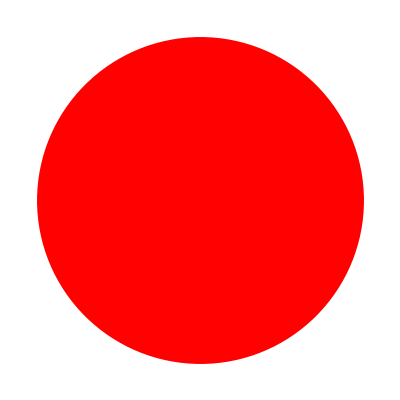
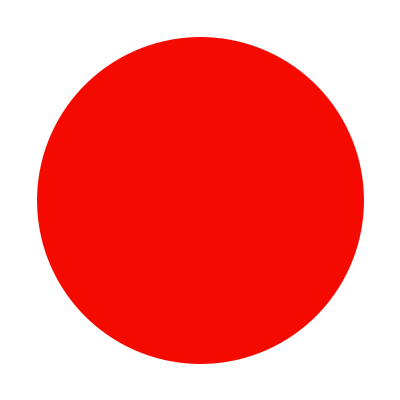
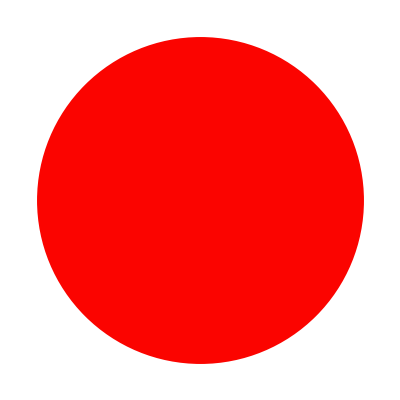
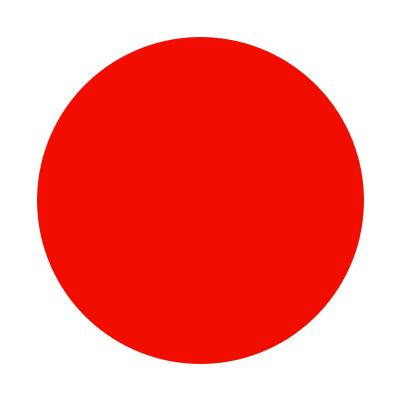
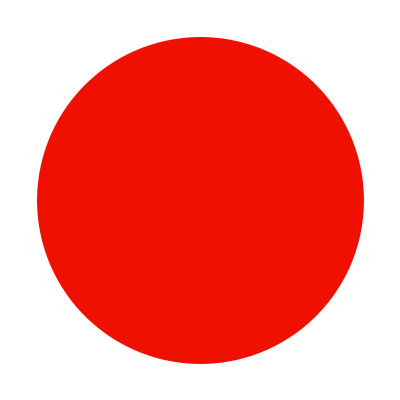
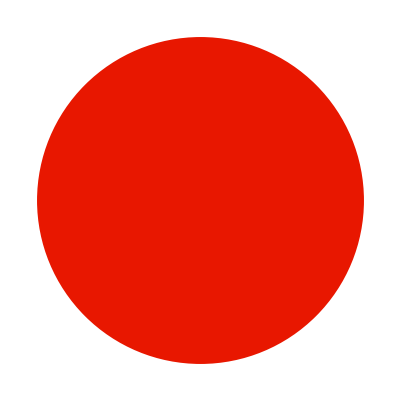
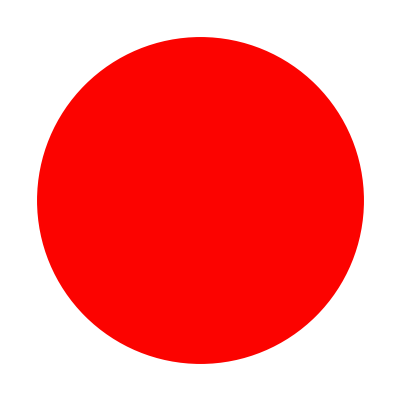
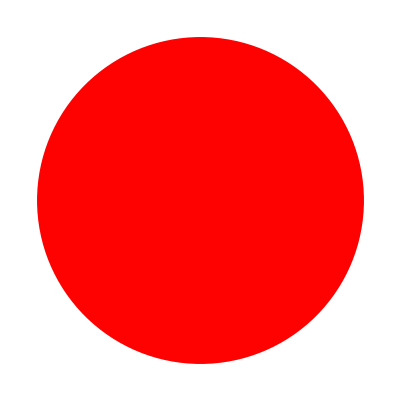
2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | 1 | 2 | 3 | 5 | 10 | 15 | 30Number of minutesNumber of threadsPercentage of accesses to Transposition Table which are Reads

```mathematica
writePercentageGraph=Module[{color,gr,gr2,gr3,realGrid,l},
color[num_]:=Module[{dat,percent,red,green},
dat=colorData[[All,All,-1]];
dat=Select[#,#≤1&]&/@dat;
percent=(num-Min@Flatten@dat)/(Max@Flatten@dat-Min@Flatten@dat);
percent=num;
RGBColor[1-percent,percent,0]
];
gr=Graphics[{color[#],Disk[{0,0},#]}]&/@#&/@colorData[[All,All,-1]];gr2=MapThread[Prepend[#,#2]&,{gr,{2,3,4,6,8,12}}];
gr3=Append[gr2,{"",1,2,3,5,10,15,30}];
gr3[[1]][[8]]="";
realGrid=Grid[gr3,Frame->{{None,{True}},{{True},None}},ItemSize->{4,4}];l=Labeled[realGrid,{"Number of minutes","Number of threads","Percentage of accesses to Transposition Table which are Reads",""},All,RotateLabel->True]
]
```

```mathematica
cd={#[[1,1]],Median@#[[All,-3;;]]}&/@colorData
```

{{2.,{0.196438,0.540191,0.0562721}},{3.,{0.206077,0.545473,0.0188472}},{4.,{0.237411,0.590791,0.0223343}},{6.,{0.260985,0.617161,0.0283131}},{8.,{0.266205,0.623931,0.0329361}},{12.,{0.258876,0.612872,0.0432553}}}

```mathematica
cd[[All,1]]
```

{2.,3.,4.,6.,8.,12.}

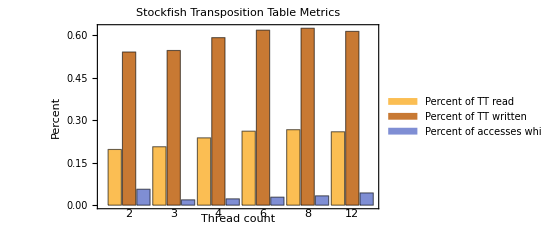

```mathematica
bc=BarChart[cd[[All,2]],ChartLabels->{Placed[Round@#&/@cd[[All,1]],Below],Placed[{"","",""},Top]},ChartLegends->{"Percent of TT read","Percent of TT written","Percent of accesses which were reads"},PlotLabel->"Stockfish Transposition Table Metrics",FrameLabel->{"Thread count","Percent"},Frame->{{True,False},{True,False}}]
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/TTmetrics.png",bc]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/TTmetrics.png

```mathematica
cd[[All,2]]
```

{{0.196438,0.540191,0.0562721},{0.206077,0.545473,0.0188472},{0.237411,0.590791,0.0223343},{0.260985,0.617161,0.0283131},{0.266205,0.623931,0.0329361},{0.258876,0.612872,0.0432553}}

```mathematica
Flatten@({#,#,#}&/@cd[[All,1]])
```

{2.,2.,2.,3.,3.,3.,4.,4.,4.,6.,6.,6.,8.,8.,8.,12.,12.,12.}

```mathematica
{Round@#}&/@cd[[All,1]]
```

{{2},{3},{4},{6},{8},{12}}